```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
Subscript[ω, 0]=1;
Subscript[ω, 1]=1/3;
b[t_]=Sqrt[1+(Subscript[ω, 0]^2-Subscript[ω, 1]^2)/Subscript[ω, 1]^2 Sin[Subscript[ω, 1]*t]^2];
τ[t_]=ArcTan[(Subscript[ω, 0] Tan[t Subscript[ω, 1]])/Subscript[ω, 1]]/Subscript[ω, 0];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[ψ, A][x_,y_,t_,κ_]=E^(I*π*(1-κ)HeavisideTheta[y-x])Subscript[ψ, F][x,y,t];
Subscript[ρ, α][x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0], {Subscript[x, 2],x, y}];
Subscript[ρ, A][x_,y_,t_,κ_]=1/b[t]*Subscript[ρ, α][x/b[t],y/b[t],κ]*E^((I*b'[t])/(2b[t])(y^2-x^2));
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
MInt[p_,t_,κ_]:=2/(2π)NIntegrate[E^(I*p*(x-y))Subscript[ρ, A][x,y,t,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->6,PrecisionGoal->6];
Subscript[n, A][p_,t_,κ_]:=Subscript[n, A][p,t,κ]=If[p≥0,
If[t≤3π/2,Re[MInt[p,t,κ]],Re[Subscript[n, A][p,3π-t,κ]]],
If[t≤3π/2,Re[Subscript[n, A][-p,t,κ]],Re[Subscript[n, A][p,3π-t,κ]]]];
```

We should see that the period of motion for the system is T = π/ω_1=3π -- so we only need to numerically simulate for 3π seconds

```mathematica
Pdomain=Union[Range[-2,0,1/5],Range[0,2,1/5],{-2.5,2.5,-3,3,-3.5,3.5,-4,4}];
Tdomain=Table[i*π/16,{i,0,48}];
```

```mathematica
Do[Map[Subscript[n, A][#,Tdomain[[i]], 0]&,Pdomain];Print[ToString[i] <>" is complete"],{i,1,Length[Tdomain]}]
```

```mathematica
Subscript[f, m_]:= Interpolation[Thread[{Pdomain,Table[Re[Subscript[n, A][Pdomain[[i]], Tdomain[[m]],0 ]],{i,1,Length[Pdomain]} ] }]];
FuncList=Table[Subscript[f, i][x],{i,1,Length[Tdomain]/2+1,4}];
```

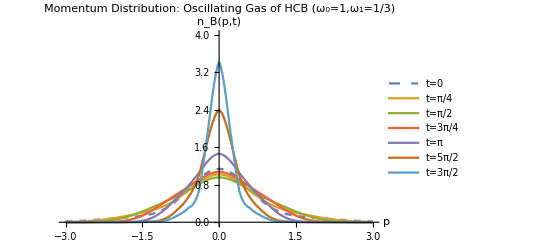

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistOscillatingTG.png

```mathematica
p1=Plot[FuncList,{x,-3,3},PlotRange->{0,4},PlotLabel->"Momentum Distribution: Oscillating Gas of HCB (ω_0=1,ω_1=1/3)",AxesLabel->{"p","n_B(p,t)"},PlotStyle->{Dashed,Default,Default,Default,Default,Default,Default},
ImageSize->Scaled[0.4], PlotLegends->{"t=0","t=π/4","t=π/2","t=3π/4","t=π","t=5π/2","t=3π/2"}]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistOscillatingTG.png",p1]
```

```mathematica
frame[i_]:=Show[Plot[Subscript[f, i][x],{x,-4,4},PlotRange->{0,4},PlotLabel->"Momentum Distribution: Oscillating Gas of HCB (ω_0=1,ω_1=1/3)",AxesLabel->{"p","n_B(p,t)"},ImageSize->Scaled[1]],Graphics[Text[StringForm["t = ``",Round[N[Tdomain[[i]]],.1 ]],{2,1},{0,0}]]];
frames=Table[frame[i],{i,0,Length[Tdomain] - 1}];
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/OscillatingTG.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .16];
```

```mathematica
Subscript[n, A][4,0,0]
```

0.0031523

```mathematica
DumpSave["C:\\Users\\Tim\\Documents\\PhysicsResearch\\UltraColdAtoms\\Code\\OscillatingHCBdump.mx","Global`"];
```

```mathematica
Table[,{i,1,Length[Tdomain]/2,4}]
```

{1/16,5/16,9/16,13/16,17/16,21/16}